```mathematica
ClearAll["Global'*"]
```

## Definitions

```mathematica
ϕ[x_]:=Piecewise[{{Exp[x]-1,x ≤0},{x,x>0}}]
[x_]:=Piecewise[{{0,x ≤0},{x,x>0}}]
ELU[x_]:= ϕ/@x
ReLU[x_]:= /@x
GELU[x_]:=x/2*(1+Erf[x/Sqrt[2]])
W0 = {{0,-1},{-1,0}};
ϵ = 1/100;
f[x_,W_]:= ReLU[W.x + {1,1}] - x
```

```mathematica
Unperturbed
```

Unperturbed

```mathematica
Solve[f[{x,y},W0]=={0,0}]
```

{{y→ConditionalExpression[1-x, 0≤x≤1]}}

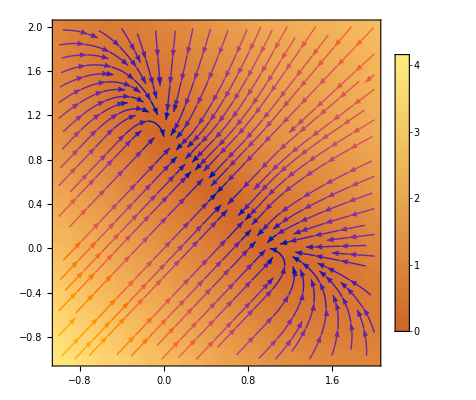

```mathematica
StreamDensityPlot[f[{x,y},W0],{x,-1,2},{y,-1,2},PlotLegends->Automatic]
```

```mathematica
Fixed perturbation of 𝒪(ϵ)= 1/1000
```

```mathematica
Δ = {{0,2ϵ},{2ϵ, 2ϵ}};
Solve[f[{x,y},W0+Δ]=={0,0}]
```

{{x→0,y→50/49}}

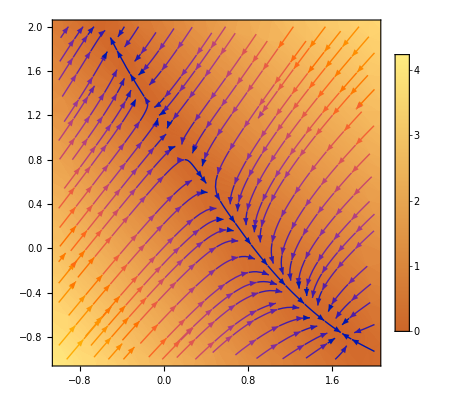

```mathematica
StreamDensityPlot[f[{x,y},W0+Δ],{x,-1,2},{y,-1,2},PlotLegends->Automatic]
```

## Random perturbation 𝒪(ϵ) = 1/1000

```mathematica
Δ = ϵ*RandomInteger[9,{2,2}]-1/2
```

{{-23/50,-12/25},{-47/100,-1/2}}

```mathematica
Solve[f[{x,y},W0+Δ]=={0,0}]
```

{{x→50/73,y→0}}

```mathematica
StreamDensityPlot[f[{x,y},W0+Δ],{x,-1,2},{y,-1,2},PlotLegends->Automatic]
```

-Graphics-

```mathematica
f[{x,y},W0+Δ]
```

{-x+(Piecewise[{{0, 1-(23 x)/50-(37 y)/25≤0}, {1-(23 x)/50-(37 y)/25, 1-(23 x)/50-(37 y)/25>0}, {0, True}}]),-y+(Piecewise[{{0, 1-(147 x)/100-y/2≤0}, {1-(147 x)/100-y/2, 1-(147 x)/100-y/2>0}, {0, True}}])}

## Nullclines

```mathematica
f1[x1_, x2_, ϵ11_,ϵ12_]:=ELU[ ϵ11*x1+(ϵ12-1)*x2 + 1] - x1
ϵ11=1/300;
ϵ12=1/200;
f1[x1_, x2_]:=ELU[ ϵ11*x1+(ϵ12-1)*x2 + 1] - x1
f1[x1_, x2_]:=ELU[ x1+ 1] - x1
```

```mathematica
reg=Reduce[ϵ11*x1+(ϵ12-1)*x2 + 1<0]&&-5<x2<5
reg
cp=ContourPlot[{f1[x,y]==0},{x,y}∈ reg];
Show[cp]
```

x2∈ℝ&&x1<1/2 (-600+597 x2)&&-5<x2<5

x2∈ℝ&&x1<1/2 (-600+597 x2)&&-5<x2<5

ContourPlot::idomdim: {x,y}∈reg does not have a valid dimension as a plotting domain.

Show::gtype: ContourPlot is not a type of graphics.

Show[ContourPlot[{f1[x,y]==0},{x,y}∈reg]]

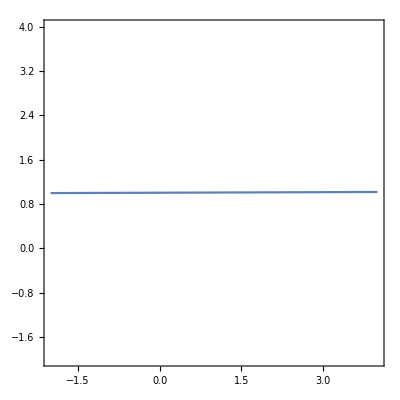

```mathematica
cp=ContourPlot[{ϵ11*x+(ϵ12-1)*y + 1==0},{x,-2,4},{y,-2,4}];
Show[cp]
```

```mathematica
cp=ContourPlot[{f1[x,y]==0},{x,-20,40},{y,-20,40}];
Show[cp]
```

-Graphics-

```mathematica
Δ = ϵ*RandomInteger[100,{2,2}]-1/2;
```

{{-317/100000,247/100000},{-59/20000,-411/100000}}

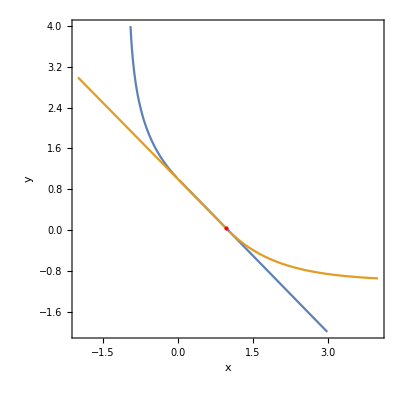

```mathematica
ϵ=1/10000;
Δ = ϵ*(RandomInteger[1000,{2,2}]-500)
f[x_,W_]:= ELU[W.x + {1,1}] - x
vp=VectorPlot[{Part[f[{x,y},W0+Δ],1],Part[f[{x,y},W0+Δ],2]},{x,-2,4},{y,-2,4},VectorScale->{0.03,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->10,VectorStyle->{GrayLevel[0.8]}];
cp=ContourPlot[{Part[f[{x,y},W0+Δ],1]==0,Part[f[{x,y},W0+Δ],2]==0},{x,-2,4},{y,-2,4}];
ptRules=NSolve[{Part[f[{x,y},W0+Δ],1]==0,Part[f[{x,y},W0+Δ],2]==0},{x,y}];
Show[vp,cp,Graphics[{Red,PointSize[Large],Point[{x,y}]/. ptRules}]]
```

```mathematica
ϵ=1/100000;

Nfixedpointslist={};
For[i=0,i<100,i++,
Δ = ϵ*(RandomInteger[1000,{2,2}]-500);
ptRules=NSolve[{Part[f[{x,y},W0+Δ],1]==0,Part[f[{x,y},W0+Δ],2]==0},{x,y}];
AppendTo[Nfixedpointslist,Length[ptRules]]
];
Counts[Nfixedpointslist]
```

$Aborted

<|1→18,3→7|>

```mathematica
Counts[Nfixedpointslist]
```

<|1→691,3→309|>

```mathematica
Nexp =10;
f[x_,W_]:= ELU[W.x + {1,1}] - x
epsarray=RandomPoint[Ball[{0,0,0,0}],Nexp];
epss=RandomReal[ {-ϵ, ϵ},Nexp];
Nfixedpointslist={};
For[i=1,i<Nexp+1,i++,
Δ = epss[[i]]*ArrayReshape[epsarray[[i]],{2,2}];
ptRules=NSolve[{Part[f[{x,y},W0+Δ],1]==0,Part[f[{x,y},W0+Δ],2]==0},{x,y}];
AppendTo[Nfixedpointslist,Length[ptRules]]
];
Counts[Nfixedpointslist]
```

$Aborted

<||>

#### Monte Carlo for “3 FP” bifurcation type

```mathematica
Nexp =10000000;
epsarray=RandomPoint[Ball[{0,0,0,0}],Nexp];
ϵ=1/100;
epss=RandomReal[ {-ϵ, ϵ},Nexp];
epscube =RandomReal[{-ϵ, ϵ},{Nexp,2,2}];
Nfixedpointslist={};
conditionssatisfiedcounter=0;
For[i=1,i<Nexp+1,i++,
Δ = ArrayReshape[epscube[[i]],{2,2}];
W =W0+Δ;
If[(Δ[[1]][[1]]*Δ[[2]][[2]]-Δ[[1]][[1]]-Δ[[2]][[2]]-Δ[[1]][[2]]*Δ[[2]][[1]]+Δ[[1]][[2]]+Δ[[2]][[1]])>0&&(Δ[[1]][[1]]<Δ[[2]][[1]])&&(Δ[[2]][[2]]<Δ[[1]][[2]]),conditionssatisfiedcounter=conditionssatisfiedcounter+1,0]
];
conditionssatisfiedcounter
```

2500160

```mathematica
ArrayReshape[epscube[[1]],{2,2}]
```

{{-0.227892,0.616809},{0.838168,-0.926241}}

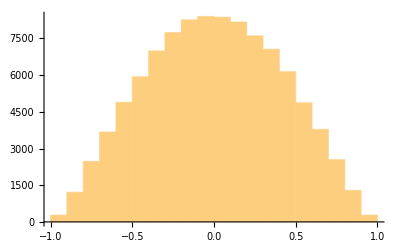

```mathematica
Histogram[epsarray[[All,1]]]
```

```mathematica
Area[a*b-a-b-c*d+c+d<0&&a<c&&a<d&&-1<a<1&&-1<b<1&&-1<c<1&&-1<d<1]
```

Area::reg: -a-b+a b+c+d-c d<0&&a<c&&a<d&&-1<a<1&&-1<b<1&&-1<c<1&&-1<d<1 is not a correctly specified region.

```mathematica
=1/10000;
RegionMeasure[ImplicitRegion[a*b-a-b-c*d+c+d>0&&a<c&&d<b&&-<a<&&-<b<&&-<c<&&-<d<,{a,b,c,d}]]/RegionMeasure[ImplicitRegion[-<a<&&-<b<&&-<c<&&-<d<,{a,b,c,d}]]
```

1/64 (8+39999999200000004 ArcCoth[10000]+19999999600000002 Log[9999]+79999998400000008 Log[10] Log[9999]+9999999800000001 Log[9999]^2+9999999800000001 Log[10000]^2-19999999600000002 Log[10001]-79999998400000008 Log[10] Log[10001]-19999999600000002 Log[9999] Log[10001]+19999999600000002 Log[10001] Log[99990000]-9999999800000001 Log[99990000]^2)

```mathematica
=1;RegionMeasure[ImplicitRegion[a*b-a-b-c*d+c+d>0&&a<c&&d<b,{{a,-,},{b,-,},{c,-,},{d,-,}}],4]/RegionMeasure[ImplicitRegion[-<a<,{{a,-,},{b,-,},{c,-,},{d,-,}}]]
```

1/8

```mathematica
RegionMeasure[ImplicitRegion[-<a<&&-<b<&&-<c<&&-<d<,{a,b,c,d}]]
```

16

```mathematica
=1/100;
RegionMeasure[ImplicitRegion[a*b-a-b-c*d+c+d<0&&a<c&&d<b&&Sqrt[a^2+b^2+c^2+d^2]<,{a,b,c,d}]]/RegionMeasure[ImplicitRegion[-<a<&&-<b<&&-<c<&&-<d<,{a,b,c,d}]]
```

$Aborted

```mathematica
RegionMeasure[ImplicitRegion[a*b-a-b-c*d+c+d<0&&a<c&&d<b&&a^2+b^2+c^2+d^2<1,{a,b,c,d}]]
```

$Aborted